DataDistribution[…]

HypothesisTestData[…]

{λ→0.0750996,τ→2062.97}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.0176545,97.6873}

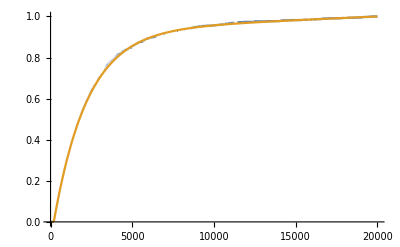

```mathematica
expcDistShape = MixtureDistribution[
{1, λ},{
TruncatedDistribution[{200, 20000},ExponentialDistribution[1/τ]],
UniformDistribution[{200, 20000}]
}];
expcDist = expcDistShape /. τ -> 2197;
data = (Transpose@Import["~/mnt/lab2/muon.tsv"])[[1]];
data = Select[data, #1 ≥ 200 &];
dist = EmpiricalDistribution[data]
DistributionFitTest[data, expcDistShape, "HypothesisTestData"]
est = FindDistributionParameters[data, expcDistShape]
estDist = expcDistShape /. est;
bootstrap:={λ,τ}/.FindDistributionParameters[RandomChoice[data,Length@data],expcDistShape];
stderrs = StandardDeviation/@Transpose@ParallelTable[bootstrap,{1000}]
Plot[{
CDF[dist, x],
CDF[estDist, x]
}, {x, 0, 20000}, PlotRange->All]
```